## Edit

Run Ca_PQ and Ca_N notebooks first, to derive Ca at all distances around a single channel; then run this notebook

```mathematica
Ctr=0;
NBlock=1;
PQBlock=0;

cluster1=0;
cluster2=0;
cluster3=0;
cluster4=0;
ring=1;
ring2=0;

CaPlot=0;
FusPlot=1;
CalPr=1;
```

## Cluster, Rings & CaT

```mathematica
ClearAll[DPQ,DN,CaPQ,CaN,CaT]
If[cluster1==1,
DPQ=Table[
j,{j,5,95,10}];
DN=Table[
j,{j,5,55,10}];]

If[cluster2==1,
DPQ=Join[Table[
j,{j,11,61,10}],Table[
j,{j,11,61,10}]];
DN=Table[
j,{j,11,71,10}];]

If[cluster3==1,
cl=16;
lo=36;
DPQ=Join[
Table[j,{j,cl,lo,10}],
Table[j,{j,cl,lo,10}],
Table[j,{j,cl,lo,10}],
Table[j,{j,cl+1,lo+1,10}]
];
DN=Join[
Table[j,{j,cl,lo,10}],
Table[j,{j,cl+1,lo+1,10}],
{lo}
];
]

If[cluster4==1,
cl=19;
lo=29;
DPQ=Join[
Table[j,{j,cl,lo,10}],
Table[j,{j,cl,lo,10}],
Table[j,{j,cl,lo,10}],
Table[j,{j,cl,lo,10}],
Table[j,{j,cl+1,lo+1,10}],
Table[j,{j,cl+1,lo+1,10}]
];
DN=Join[
Table[j,{j,cl,lo,10}],
Table[j,{j,cl,lo,10}],
Table[j,{j,cl+1,lo+1,10}],
{lo+1}
];
]

If[ring==1,
dist=40;       (*36 for Syt1n*)
DPQ=Table[dist,6];
DN=Table[dist,1]
];
(*values for 200 shells in Ca_PQ and Ca_N*)
If[ring2==1,
distPQ=15; (*κS 120: 21; κS 25: 16; κS 7: 15;*)
distN=distPQ+24;  (*κS 120: +12; κS 25: +23; κS 7: +24; *)
DPQ=Table[distPQ,6];(*κS 120: 12; κS==25: NPQ=7; κS==7: NPQ=6;*)
DN=Table[distN,4]  (*κS 120: 7; κS==25: NN=5; κS==7: NN=4; *)
];

DPQ
DN

CaPQ=Sum[Ca[i][t],{i,DPQ}];
CaN=Sum[Can[i][t],{i,DN}];

If[Ctr==1,
CaT=CaPQ+CaN];
If[NBlock==1,
CaT=CaPQ];
If[PQBlock==1,
CaT=CaN];


If[CaPlot==1,
Plot[
Evaluate[
10^3*CaT/. sol/.soln], {t, 0., TimeWindow},PlotRange->All]]
```

{40,40,40,40,40,40}

{40}

## Release

### Edit

```mathematica
Schnegg=0; (*Schneggenburger & Nehr, 2000 model*)
SchneggY=0; (*Kochubey model for young; select Schnegg =1 + SchneggY = 1*)
SchneggA=0;(*Kochubey model for adult; select Schnegg =1 + SchneggA = 1*)
Syt1prim=1; (*new Syt1 priming model*)
Syt1n=0; (*new Syt1 model*)
```

### Parmeters

```mathematica
If[Syt1prim==1,
R1size=1.;
Vtotal=1.;
n=5;
Km=20.*10^-3;
v=6000.;
vb=0.;
kOffV=10000.;
kOnV=1.*10^5;
a=4;
g=4000.;
]

If[Syt1n==1,
Vtotal=1.;
kOffV=10000.;
kOnV=1.*10^5;
a=4.;
g=5900.;
]

If[SchneggY==1,
kOffV=6500;
kOnV=1.21*10^5;
b=0.26;
g=6960;
]

If[SchneggA==1,
kOffV=7900;
kOnV=1.15*10^5;
b=0.26;
g=6960;
]
```

### Resting conditions

```mathematica
Vtotal=1.0;

If[Schnegg==1,
RuheV=Join[
(* t=0 equations *)
{RestV[0]==Vtotal},
{RestCaV[0]==0},
{RestCa2V[0]==0},
{RestCa3V[0]==0},
{RestCa4V[0]==0},
{RestCa5V[0]==0},

(* f' equations *)
{RestV'[x]==-(RestCaV'[x]+RestCa2V'[x]+RestCa3V'[x]+RestCa4V'[x]+RestCa5V'[x])},
{RestCaV'[x]==5*kOnV*CaRest*RestV[x] - kOffV *RestCaV[x]},
{RestCa2V'[x]==4*kOnV*CaRest* RestCaV[x] - 2*b*kOffV *RestCa2V[x]},
{RestCa3V'[x]==3*kOnV*CaRest*RestCa2V[x] - 3*b^2 *kOffV *RestCa3V[x]},
{RestCa4V'[x]==2*kOnV*CaRest* RestCa3V[x] - 4*b^3*kOffV *RestCa4V[x]},
{RestCa5V'[x]==kOnV*CaRest* RestCa4V[x] - 5*b^4*kOffV *RestCa5V[x]}
];

solV := NDSolve[RuheV,{RestV,RestCaV,RestCa2V,RestCa3V,RestCa4V,RestCa5V},{x,0.,1.}]; 

IniV = Extract[RestV[1.]/.solV,1];
IniCaV = Extract[RestCaV[1.]/.solV,1];
IniCa2V = Extract[RestCa2V[1.]/.solV,1];
IniCa3V = Extract[RestCa3V[1.]/.solV,1];
IniCa4V = Extract[RestCa4V[1.]/.solV,1];
IniCa5V = Extract[RestCa5V[1.]/.solV,1];
]
```

### Sensor models and solving

```mathematica
(*ClearAll[Vars1,Eqns1]*)
ClearAll[Fusion,VarsSensor,Eqns1,Vars1,sol1,FusRate]

If[Schnegg==1,
Fusion:=Join[
(* t=0 equations *)
{V[0]==IniV},
{CaV[0]==IniCaV},
{Ca2V[0]==IniCa2V},
{Ca3V[0]==IniCa3V},
{Ca4V[0]==IniCa4V},
{Ca5V[0]==IniCa5V},
{Fus[0]==0},

{V'[t]==-5*kOnV*CaT* V[t] + kOffV *CaV[t]},
{CaV'[t]==5*kOnV*CaT* V[t] - kOffV *CaV[t]-4*kOnV*CaT* CaV[t] +2* b*kOffV *Ca2V[t]},
{Ca2V'[t]==4*kOnV*CaT* CaV[t] -2* b*kOffV *Ca2V[t]-3*kOnV*CaT* Ca2V[t] + 3*b^2 *kOffV *Ca3V[t]},
{Ca3V'[t]==3*kOnV*CaT* Ca2V[t] - 3*b^2 *kOffV *Ca3V[t]-2*kOnV*CaT* Ca3V[t] + 4*b^3*kOffV *Ca4V[t]},
{Ca4V'[t]==2*kOnV*CaT* Ca3V[t] - 4*b^3*kOffV *Ca4V[t]-kOnV*CaT* Ca4V[t] + 5*b^4*kOffV *Ca5V[t]},
{Ca5V'[t]==kOnV*CaT* Ca4V[t] - 5*b^4*kOffV *Ca5V[t]-Fus'[t]},
{Fus'[t]==g*Ca5V[t]}
]
];

If[Schnegg==1,
Fusion=Flatten[Fusion];

VarsSensor = 
Join[
{V,CaV,Ca2V,Ca3V,Ca4V,Ca5V,Fus}];

VarsSensor=Flatten[VarsSensor];



Eqns1 =Flatten[Join[Eqns,FreeCan,{Fusion}]];
Vars1=Flatten[Join[Vars,VarFreeCan, {VarsSensor}]];

sol1 = NDSolve[Eqns1,Vars1,{t,0.,TimeWindow},Method->{"EquationSimplification"->"Solve"}];


FusRate=Evaluate[(Fus'[t])/.sol1];

]


If[Syt1prim==1,
Fusion:=Join[
(* t=0 equations *)

{R1[0]==R1size},
{V[0]==Vtotal},
{CaV[0]==0},
{Ca2V[0]==0},
{Ca3V[0]==0},
{Ca4V[0]==0},
{Ca5V[0]==0},
{Fus[0]==0},

{R1'[t]==-v*(CaT^n/(CaT^n+Km^n))*R1[t]+vb*V[t]},
{V'[t]==-5*kOnV*CaT* V[t] + kOffV *CaV[t]+v*(CaT^n/(CaT^n+Km^n))*R1[t]-vb*V[t]},
{CaV'[t]==5*kOnV*CaT* V[t] - kOffV *CaV[t]-4*a kOnV*CaT* CaV[t] +2* kOffV *Ca2V[t]},
{Ca2V'[t]==4*a kOnV*CaT* CaV[t] -2* kOffV *Ca2V[t]-3*a^2 kOnV*CaT* Ca2V[t] + 3*kOffV *Ca3V[t]},
{Ca3V'[t]==3*a^2 kOnV*CaT* Ca2V[t] - 3*kOffV *Ca3V[t]-2*a^3 kOnV*CaT* Ca3V[t] + 4*kOffV *Ca4V[t]},
{Ca4V'[t]==2*a^3 kOnV*CaT* Ca3V[t] - 4*kOffV *Ca4V[t]-a^4 kOnV*CaT* Ca4V[t] + 5*kOffV *Ca5V[t]},
{Ca5V'[t]==a^4 kOnV*CaT* Ca4V[t] - 5*kOffV *Ca5V[t]-Fus'[t]},
{Fus'[t]==g*Ca5V[t]}
]];

If[Syt1prim==1,
Fusion=Flatten[Fusion];

VarsSensor = 
Join[
{R1,V,CaV,Ca2V,Ca3V,Ca4V,Ca5V,Fus}];

VarsSensor=Flatten[VarsSensor];
Eqns1 =Flatten[Join[Eqns,{Fusion}]];
Vars1=Flatten[Join[Vars, {VarsSensor}]];
sol1 = NDSolve[Eqns1,Vars1,{t,0.,TimeWindow},Method->{"EquationSimplification"->"Residual"}];

FusRate=Evaluate[(Fus'[t])/.sol1];

]

If[Syt1n==1,
Fusion:=Join[
(* t=0 equations *)

{V[0]==Vtotal},
{CaV[0]==0},
{Ca2V[0]==0},
{Ca3V[0]==0},
{Ca4V[0]==0},
{Ca5V[0]==0},
{Fus[0]==0},

{V'[t]==-5*kOnV*CaT* V[t] + kOffV *CaV[t]},
{CaV'[t]==5*kOnV*CaT* V[t] - kOffV *CaV[t]-4*a kOnV*CaT* CaV[t] +2* kOffV *Ca2V[t]},
{Ca2V'[t]==4*a kOnV*CaT* CaV[t] -2* kOffV *Ca2V[t]-3*a^2 kOnV*CaT* Ca2V[t] + 3*kOffV *Ca3V[t]},
{Ca3V'[t]==3*a^2 kOnV*CaT* Ca2V[t] - 3*kOffV *Ca3V[t]-2*a^3 kOnV*CaT* Ca3V[t] + 4*kOffV *Ca4V[t]},
{Ca4V'[t]==2*a^3 kOnV*CaT* Ca3V[t] - 4*kOffV *Ca4V[t]-a^4 kOnV*CaT* Ca4V[t] + 5*kOffV *Ca5V[t]},
{Ca5V'[t]==a^4 kOnV*CaT* Ca4V[t] - 5*kOffV *Ca5V[t]-Fus'[t]},
{Fus'[t]==g*Ca5V[t]}
]

];


If[Syt1n==1,
Fusion=Flatten[Fusion];

(*VarsSensor = 
Join[
{V,CaV,Ca2V,Ca3V,Ca4V,Ca5V,Fus}];

VarsSensor=Flatten[VarsSensor];
Eqns1 =Flatten[Join[Eqns,{Fusion}]];
Vars1=Flatten[Join[Vars, {VarsSensor}]];
sol1 = NDSolve[Eqns1,Vars1,{t,0.,TimeWindow},Method->{"EquationSimplification"->"Residual"}];

FusRate=Evaluate[(Fus'[t])/.sol1];*)

VarsSensor = 
Join[
{V,CaV,Ca2V,Ca3V,Ca4V,Ca5V,Fus}];

VarsSensor=Flatten[VarsSensor];
Eqns1 =Flatten[Join[Eqns,FreeCan,{Fusion}]];
Vars1=Flatten[Join[Vars,VarFreeCan, {VarsSensor}]];
sol1 = NDSolve[Eqns1,Vars1,{t,0.,TimeWindow},Method->{"EquationSimplification"->"Solve"}];


FusRate=Evaluate[(Fus'[t])/.sol1];

]
```

### Plotting

Syt1 priming model

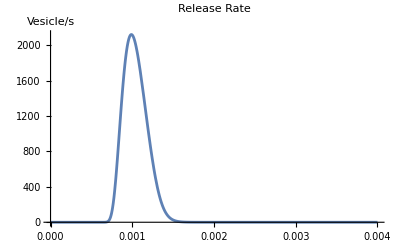

```mathematica
If[SchneggA==1,Print["Schnegg adult Model"]]
If[SchneggY==1,Print["Schnegg young Model"]]
If[Syt1prim==1,Print["Syt1 priming model"]]
If[Syt1n==1,Print["Syt1 model"]]


If[FusPlot==1,
p1=Plot[FusRate,{t,0,TimeWindow},PlotRange->All,AxesLabel->"Vesicle/s",PlotLabel->"Release Rate"]
]
```

### Calculating pr

```mathematica
Clear[pr1]
pr1=NIntegrate[{FusRate},{t,0.0006,0.004}];

If[Syt1prim==1,
pr1/=1.98,pr1];

pr1=Flatten[pr1];
Column[pr1," "]
```

0.383869